```mathematica
size = 1024;
Do[
beta = 5 - 2*dim;
phase = Table[Exp[ 1.0 I Random[Real, N[2 Pi]]],{v,1,size}];
phase[[1]] = phase[[size / 2 + 1]] = 1;
Do [phase[[size-q+2]] = Conjugate[ phase[[q]] ], {q,2,size/2}];
spect = phase * Table[N[1/k^(beta/2)],{k,1,size}];
brown = Re[Fourier[spect]];
brownPl = ListPlot[brown, Joined->True, Axes->None],
{dim,1.1,1.9,0.2}
]
```

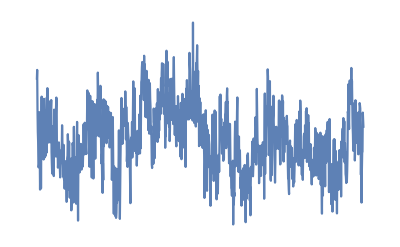

```mathematica
Show[brownPl]
```